```mathematica
Directory[]
```

/Users/alexis/workspace/clustersearch/cpp/build

```mathematica
SetDirectory["/Users/alexis/workspace/clustersearch/cpp/build"]
```

/Users/alexis/workspace/clustersearch/cpp/build

This function wraps the program “clusters”

```mathematica
Clusters[alpha_,length_,colors_,gray_,samples_]:=
(* Returns means of cluster_size, perimeter_size, colors, exits_size, robustness *)
Block[{args,command,seed=0},
args="";
args = StringJoin[args," ", "--alpha=",     ToString[alpha]];
args = StringJoin[args," ", "--length=",   ToString[length]];
args = StringJoin[args," ", "--colors=",   ToString[colors]];
args = StringJoin[args," ", "--gray=",       ToString[gray]];
args = StringJoin[args," ", "--samples=", ToString[samples]];
args = StringJoin[args," ", "--seed=",       ToString[seed]];
args = StringJoin[args," ", "--verbose=0"];
command=StringJoin["!./clusters",args];
Flatten @ ReadList[command,Number,RecordLists->True]]
```

For example, we can search one cluster given binary length-10 strings with 4 colors:.

```mathematica
Clusters[2,10,4,0,1]
```

{240,691,3,1718,0.284167}

These help with displaying tabular output from multiple calls to Clusters

```mathematica
(* Headings of Clusters output, for labelling tabular displays.

For example:
 TableForm[<output>,TableHeadings->{None,ClustersHeadingsShort},TableAlignments->"."];
   Grid[%129~Prepend~ClustersHeadingsShort,Alignment->"."];
 *)
ClustersHeadingsShort=
{"s","t","E","u","r"};
ClustersHeadingsLong={"cluster_size","perimeter_size","colors_seen","exits_size","robustness"};
```

```mathematica
ClustersTableForm[table_]:=
TableForm[table,TableHeadings->{None,ClustersHeadingsShort},TableAlignments->"."]
```

An example

Suppose that I want to
hold constant
   alpha =2
   length=10 
   samples = 15
   gray=0

let 
  colors range from 2 to 5,
 
and generate a table of  outputs from Clusters

```mathematica
(* Generate table ranging over colors from 2..5 *)
With[{alpha=2,length=8,samples=100,gray=0},
Table[Clusters[alpha,length,colors,gray,samples],
{colors,2,5}]]
```

{{126.58,125.85,1,503.58,0.496301},{74.45,148.44,2,386.32,0.325612},{38.43,112.36,2.99,215.6,0.237349},{15.93,62.35,3.96,93.76,0.191666}}

Display it as a table with headings

```mathematica
ClustersTableForm[%]
```

s | t | E | u | r
126.58 | 125.85 | 1 | 503.58 | 0.496301
74.45 | 148.44 | 2 | 386.32 | 0.325612
38.43 | 112.36 | 2.99 | 215.6 | 0.237349
15.93 | 62.35 | 3.96 | 93.76 | 0.191666

Suppose I want to generate the same table as below, but left-joining a column of colors

```mathematica
(* Generate table ranging over colors from 2..5 *)
With[{alpha=2,length=8,samples=10,gray=0},
Table[{colors}~Join~Clusters[alpha,length,colors,gray,samples],
{colors,2,5}]]
```

{{2,126.9,127.7,1,508,0.497934},{3,66.6,132.9,2,347.4,0.294298},{4,44.6,126.6,3,245.4,0.272793},{5,19.1,70.2,3.9,111.2,0.175014}}

Display it as a table with headings, adding a new heading m for colors allowed.

```mathematica
ClustersTableFormRanging[table_,rangeHeader_]:=
(* Clusters output, with a ranging input var in left col *)
TableForm[table,
TableHeadings->{None,{rangeHeader}~Join~ClustersHeadingsShort},
TableAlignments->"."]
```

```mathematica
ClustersTableFormRanging[%%,"m"]
```

m | s | t | E | u | r
2 | 126.9 | 127.7 | 1 | 508 | 0.497934
3 | 66.6 | 132.9 | 2 | 347.4 | 0.294298
4 | 44.6 | 126.6 | 3 | 245.4 | 0.272793
5 | 19.1 | 70.2 | 3.9 | 111.2 | 0.175014

We use this pick out columns to prepare arguments for ListPlot

```mathematica
PickColumn1andCol[table_,col]:=
(* Picks cols 1 and COL from table *)
Map[( #[[{1,col}]] & ),table]
```

```mathematica
PickColumn1andColumnX[%228,6]
```

{{2,0.497934},{3,0.294298},{4,0.272793},{5,0.175014}}

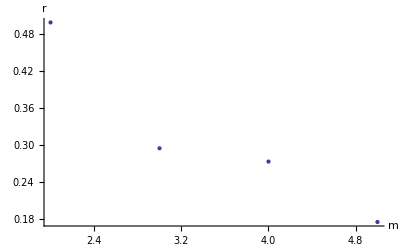

```mathematica
ListPlot[%,AxesLabel->{m,r}]
```

Now let’s do some analysis
ranging 
  colors from 2 ... 32.
with
  length=8
  alpha=2

```mathematica
(* Generate table ranging over colors from 2..5 *)
data = With[{alpha=2,length=8,samples=10,gray=0},
Table[{colors}~Join~Clusters[alpha,length,colors,gray,samples],
{colors,2,32}]]
```

{{2,126.9,127.7,1,508,0.497934},{3,66.6,132.9,2,347.4,0.294298},{4,44.6,126.6,3,245.4,0.272793},{5,19.1,70.2,3.9,111.2,0.175014},{6,9.4,38.4,4.8,54.6,0.130894},{7,12.3,53.1,5.9,73.6,0.185551},{8,5.8,28.6,6.2,36.6,0.106845},{9,4.1,22.4,6.8,26,0.129186},{10,2.5,15.7,6.6,17,0.0808333},{11,2.1,13.9,7.3,14.6,0.0804167},{12,4.1,23,8.4,26.4,0.139744},{13,2,13.2,7.7,13.8,0.0708333},{14,2.4,14.8,8.3,16.2,0.0708333},{15,1.2,9.2,6.9,9.2,0.025},{16,2.9,18,9.5,19.2,0.115833},{17,1.9,12.7,8.4,13.4,0.0505952},{18,1.5,10.7,7.8,11,0.0354167},{19,2,13.5,9.3,14,0.0791667},{20,1.5,10.8,8.4,11,0.0458333},{21,1.6,11.5,8.8,11.6,0.0666667},{22,1.3,9.8,7.7,9.8,0.0375},{23,1.2,9.1,7.6,9.2,0.0166667},{24,1.8,12.7,9.8,12.8,0.0916667},{25,1.1,8.6,6.9,8.6,0.0125},{26,1.2,9.2,7.9,9.2,0.025},{27,1.3,9.6,7.6,9.8,0.01875},{28,1.5,10.8,9,11,0.0458333},{29,1.5,10.9,8.9,11,0.0541667},{30,1.1,8.6,7.5,8.6,0.0125},{31,1.2,9.2,8.1,9.2,0.025},{32,1.2,9.2,8.1,9.2,0.025}}

```mathematica
Length[data]
```

31